```mathematica
两个矩形脉冲的数值相关
```

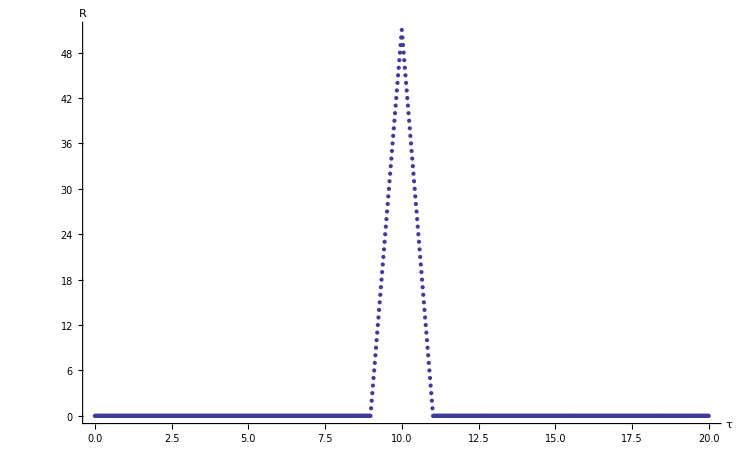

```mathematica
y[t_]:=UnitStep[(t-10)*(11-t)];
x[t_]:=UnitStep[t*(1-t)];
sample=1000;tm=20.0;
ysequence=Table[y[t],{t,0,tm,tm/sample}];
xsequence=Table[x[t],{t,0,tm,tm/sample}];
corr=ListCorrelate[xsequence,ysequence,1,0];
len=Length[corr];
corr=Table[{(j-1) tm/sample,corr[[j]]},
{j,len}];
ListPlot[corr,PlotRange->All,
AxesStyle->Thickness[0.003],
PlotStyle->Thickness[0.004],
AxesLabel->{"τ","R"},
BaseStyle->{FontSize->13}]
Clear[x,g,sample,ysequence,xsequence,corr]
```